## Create points

Uncomment the one you want to use. The results should be the same.

```mathematica
EvenlySpacedPointsFactory[points,0,1,50,z]
(*CollocationPointsFactory[points,0,1,50,z]*)
points[z]
```

{0.,0.0204082,0.0408163,0.0612245,0.0816327,0.102041,0.122449,0.142857,0.163265,0.183673,0.204082,0.22449,0.244898,0.265306,0.285714,0.306122,0.326531,0.346939,0.367347,0.387755,0.408163,0.428571,0.44898,0.469388,0.489796,0.510204,0.530612,0.55102,0.571429,0.591837,0.612245,0.632653,0.653061,0.673469,0.693878,0.714286,0.734694,0.755102,0.77551,0.795918,0.816327,0.836735,0.857143,0.877551,0.897959,0.918367,0.938776,0.959184,0.979592,1.}

## Plots

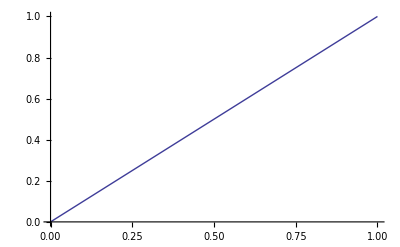

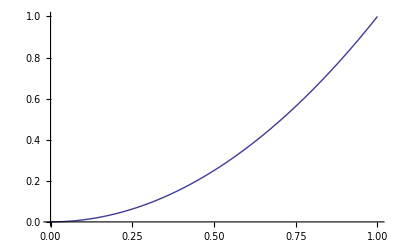

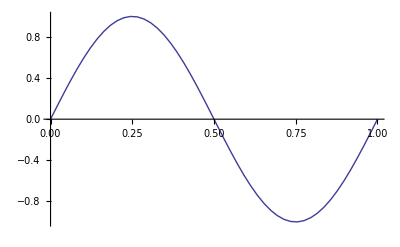

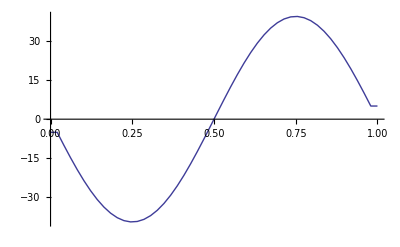

```mathematica
points[plot][points[z]]
points[plot][points[z]^2]
points[plot][Sin[2π points[z]]]
points[plot][points[diff][Sin[2π points[z]],2],PlotRange->All]
```

## Other features

50

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

True

InterpolatingFunction[{{0.,1.}},<>]

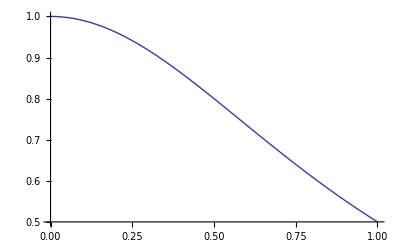

```mathematica
points[number]
points[zeroes]
points[ones]
(* Spacing does not exist for collocation points*)
points[spacing]==points[z][[2]]-points[z][[1]] 
points[interpolation][1/(1+points[z]^2)]
Plot[%[z],{z,0,1}]
```

## Integrate

```mathematica
points[plot][points[integrate][points[ones]]]
```

-Graphics-

## Interpolate and evaluate

```mathematica
points[evaluate][points[z]^2,{0.1,0.2,0.3}]
```

{0.01,0.04,0.09}

## If you have some equation of a function f[z] that you wish to discretise:

```mathematica
z f'[z]+f[z]/.points[substituteAnalytic][{f}]
```

{0.+f[1],f[2]+0.0204082 (-49. f[1]+49. f[2]),f[3]+0.0408163 (-49. f[2]+49. f[3]),f[4]+0.0612245 (-49. f[3]+49. f[4]),f[5]+0.0816327 (-49. f[4]+49. f[5]),f[6]+0.102041 (-49. f[5]+49. f[6]),f[7]+0.122449 (-49. f[6]+49. f[7]),f[8]+0.142857 (-49. f[7]+49. f[8]),f[9]+0.163265 (-49. f[8]+49. f[9]),f[10]+0.183673 (-49. f[9]+49. f[10]),f[11]+0.204082 (-49. f[10]+49. f[11]),f[12]+0.22449 (-49. f[11]+49. f[12]),f[13]+0.244898 (-49. f[12]+49. f[13]),f[14]+0.265306 (-49. f[13]+49. f[14]),f[15]+0.285714 (-49. f[14]+49. f[15]),f[16]+0.306122 (-49. f[15]+49. f[16]),f[17]+0.326531 (-49. f[16]+49. f[17]),f[18]+0.346939 (-49. f[17]+49. f[18]),f[19]+0.367347 (-49. f[18]+49. f[19]),f[20]+0.387755 (-49. f[19]+49. f[20]),f[21]+0.408163 (-49. f[20]+49. f[21]),f[22]+0.428571 (-49. f[21]+49. f[22]),f[23]+0.44898 (-49. f[22]+49. f[23]),f[24]+0.469388 (-49. f[23]+49. f[24]),f[25]+0.489796 (-49. f[24]+49. f[25]),f[26]+0.510204 (-49. f[25]+49. f[26]),f[27]+0.530612 (-49. f[26]+49. f[27]),f[28]+0.55102 (-49. f[27]+49. f[28]),f[29]+0.571429 (-49. f[28]+49. f[29]),f[30]+0.591837 (-49. f[29]+49. f[30]),f[31]+0.612245 (-49. f[30]+49. f[31]),f[32]+0.632653 (-49. f[31]+49. f[32]),f[33]+0.653061 (-49. f[32]+49. f[33]),f[34]+0.673469 (-49. f[33]+49. f[34]),f[35]+0.693878 (-49. f[34]+49. f[35]),f[36]+0.714286 (-49. f[35]+49. f[36]),f[37]+0.734694 (-49. f[36]+49. f[37]),f[38]+0.755102 (-49. f[37]+49. f[38]),f[39]+0.77551 (-49. f[38]+49. f[39]),f[40]+0.795918 (-49. f[39]+49. f[40]),f[41]+0.816327 (-49. f[40]+49. f[41]),f[42]+0.836735 (-49. f[41]+49. f[42]),f[43]+0.857143 (-49. f[42]+49. f[43]),f[44]+0.877551 (-49. f[43]+49. f[44]),f[45]+0.897959 (-49. f[44]+49. f[45]),f[46]+0.918367 (-49. f[45]+49. f[46]),f[47]+0.938776 (-49. f[46]+49. f[47]),f[48]+0.959184 (-49. f[47]+49. f[48]),f[49]+0.979592 (-49. f[48]+49. f[49]),f[50]+1. (-49. f[49]+49. f[50])}